# Studying stability of PF in UV limits

## Resources

```mathematica
RustBindingsPath="/Users/valentin/Documents/MG5/3.0.2.py3/PLUGIN/alphaloop/Mathematica";
AlphaLoopPath="/Users/valentin/Documents/MG5/3.0.2.py3/PLUGIN/alphaloop";
```

```mathematica
(*Get[RustBindingsPath<>"/"<>"RustFromMathematica.m"]*)
Get[RustBindingsPath<>"/"<>"RustFromMathematicaV2.m"]
```

Package for accessing alphaLoop implementation in Rust.
This V2 version uses the faster approach of StartExternalSession[Python] to talk to alphaLoop.

Variables you may want to overwrite are:

RFM$LTDFolder = <Path>;
RFM$PythonInterpreter = <Path>;
RFM$CUBAPath = <Path>;
RFM$SCSPath=<Path>;
RFM$ECOSPath=<Path>;

The function: 
RFM$GetLTDHook[name_,OptionsPattern[
{
RunMode->'LTD',
HyperparametersPath->'LTD/hyperparameters.yaml',
TopologiesPath->'LTD/topologies.yaml',
AmplitudesPath->'LTD/anplitudes.yaml',
DEBUG->False
}

Allows you to generate a hook, which will automatically be placed in the list:

RFM$AllHooksStarted

Then you can test that one hook is active with:

RFM$CheckHookStatus[hook_]

And use them to access information from Rust with the following three API entry points (for now):

RFM$GetLTDDeformation[hook_, RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetCrossSectionDeformation[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetRescaling[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$Parameterize[hook_,LoopIndex_,ECM_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$InvParameterize[hook_,LoopIndex_,ECM_,Momentum_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$Evaluate[hook_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateCut[hook_,CutID_,scalingFactor_, scalingFactorJacobian_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateIntegrand[hook_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]

Set your environment variables as follows:

RFM$CUBAPath = "<PATHTO>/Cuba-4.2/lib";
RFM$SCSPath="<PATHTO>/scs/out";
RFM$ECOSPath="<PATHTO>/ecos";
RFM$DYLDPATHS=RFM$CUBAPath<>":"<>RFM$SCSPath<>":"<>RFM$ECOSPath;

and then call:
RFM$SetEnvironment[];

Specify the running process path for the desired . It can be generated with the following command:

./bin/mg5_aMC --mode=alphaloop PLUGIN/alphaloop/validation/scalar_integrals/4L/2x2_fishnet_LTD.aL
./bin/mg5_aMC --mode=alphaloop PLUGIN/alphaloop/validation/scalar_integrals/4L/2x2_fishnet_PF.aL

./bin/mg5_aMC --mode=alphaloop PLUGIN/alphaloop/validation/scalar_integrals/2L/2L6PA.aL
./bin/mg5_aMC --mode=alphaloop PLUGIN/alphaloop/validation/scalar_integrals/2L/2L6PA_PF.aL

```mathematica
ProcessPathFishnet2x2LTD="/Users/valentin/Documents/MG5/3.0.2.py3/TEST_SCALAR_INTEGRAL_2x2_FISHNET_LTD";
ProcessPathFishnet2x2PF="/Users/valentin/Documents/MG5/3.0.2.py3/TEST_SCALAR_INTEGRAL_2x2_FISHNET_PF";
ProcessPath2L6PLTD="/Users/valentin/Documents/MG5/3.0.2.py3/TEST_SCALAR_INTEGRAL_2L_2L6PA_rank2_LTD";
ProcessPath2L6PPF="/Users/valentin/Documents/MG5/3.0.2.py3/TEST_SCALAR_INTEGRAL_2L_2L6PA_rank2_PF";
```

Specify the LTD folder to the hook package:

```mathematica
RFM$LTDFolder=AlphaLoopPath;
```

Also specify here your additional dependencies for the libraries alphaLoop depends on

```mathematica
RFM$CUBAPath = "/Users/valentin/Documents/HEP_softs/Cuba-4.2/lib";
RFM$SCSPath="/Users/valentin/Documents/HEP_softs/scs/out";
RFM$ECOSPath="/Users/valentin/Documents/HEP_softs/ecos";
RFM$LTDFolder=AlphaLoopPath;
RFM$DYLDPATHS=RFM$CUBAPath<>":"<>RFM$SCSPath<>":"<>RFM$ECOSPath;
RFM$SetEnvironment[]
```

Make sure a stat folder exists in the local directory:

```mathematica
If[Not[DirectoryQ[NotebookDirectory[]<>"/stats"]],CreateDirectory[NotebookDirectory[]<>"stats"]];
```

```mathematica
MyPrint[msg_]:=Block[{},Pause[0.1];Print[Style[msg,FontFamily->"Monaco"]]]
```

Get the hook to various deformation functional choices

First clean up all existing ones

```mathematica
GetHook[processPath_,yamlPath_,OptionsPattern[{hyperparameters->"hyperparameters.yaml",DEBUG->False}]]:=Block[{},
RFM$GetLTDHook[yamlPath,
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>OptionValue[hyperparameters],
DEBUG->OptionValue[DEBUG],
MGNumeratorPath->processPath
]
]
```

```mathematica
RefreshHooks[]:=Module[{},
RFM$KillAllHooks[];
HookFishnet2x2LTD=GetHook[ProcessPathFishnet2x2LTD,ProcessPathFishnet2x2LTD<>"/Rust_inputs/scalar_integral_4L_2x2_fishnet.yaml",
hyperparameters->"hyperparameters.yaml"];
HookFishnet2x2PF=GetHook[ProcessPathFishnet2x2PF,ProcessPathFishnet2x2PF<>"/Rust_inputs/scalar_integral_4L_2x2_fishnet.yaml",
hyperparameters->"hyperparameters.yaml"];
Hook2L6PLTD=GetHook[ProcessPath2L6PLTD,ProcessPath2L6PLTD<>"/Rust_inputs/scalar_integral_2L_2L6PA_LTD.yaml",
hyperparameters->"hyperparameters.yaml"];
Hook2L6PPF=GetHook[ProcessPath2L6PPF,ProcessPath2L6PPF<>"/Rust_inputs/scalar_integral_2L_2L6PA_PF.yaml",
hyperparameters->"hyperparameters.yaml"];
{
RFM$CheckHookStatus[HookFishnet2x2LTD],
RFM$CheckHookStatus[HookFishnet2x2PF],
RFM$CheckHookStatus[Hook2L6PLTD],
RFM$CheckHookStatus[Hook2L6PPF]
}
]
```

```mathematica
RefreshHooks[]
```

{True,True,True,True}

Set below the desired point density for the heat maps

```mathematica
HeatMapDensity=10;
```

And for the vector fields:

```mathematica
VectorFieldDensity=20;
```

Useful 3D euclidean norm

```mathematica
VDot[k_]:=k⟦1⟧^2+k⟦2⟧^2+k⟦3⟧^2
```

```mathematica
RFM$EvaluateIntegrand[HookFishnet2x2LTD,Table[0.02*ii,{ii,1,12}]]
```

-1.79132×10^-19+3.10679×10^-53 ⅈ

```mathematica
RFM$EvaluateIntegrand[HookFishnet2x2PF,Table[0.02*ii,{ii,1,12}]]
```

-1.79132×10^-19+3.10679×10^-53 ⅈ

```mathematica
RFM$EvaluateIntegrand[Hook2L6PLTD,Table[0.0002*ii,{ii,1,6}]]
```

-4.38977×10^-21+3.70188×10^-20 ⅈ

```mathematica
RFM$EvaluateIntegrand[Hook2L6PPF,Table[0.0002*ii,{ii,1,6}]]
```

4.15652×10^-19-2.19107×10^-20 ⅈ

## Rendering Tools

### Commons

Common resources below

```mathematica
ScannedMomenta[λ_,nloops_,OptionsPattern[{Incr->1}]]:=N[Table[λ{i*3+OptionValue[Incr],i*3+2*OptionValue[Incr],i*3+3*OptionValue[Incr]},{i,0,nloops-1}]];
```

```mathematica
MakeALabeledPoint[location_,label_]:=Block[{},
{Graphics[{PointSize->0.01,Red, Point[location]}],Graphics[{Red,FontSize->15,Text[label,location+{0.1,-0.01}]}]}
]
```

```mathematica
GetRescaling[hook_,moms_]:=Block[{RescalingSolutions},
RescalingSolutions=RFM$GetRescaling[hook,0,moms];
Print[RescalingSolutions];
If[RescalingSolutions["tSolutions"]⟦1⟧>0,
{RescalingSolutions["tSolutions"]⟦1⟧,RescalingSolutions["tJacobians"]⟦1⟧},
{RescalingSolutions["tSolutions"]⟦2⟧,RescalingSolutions["tJacobians"]⟦2⟧}
]
]
```

```mathematica
RefreshHooks[]
```

{True,True,True,True}

```mathematica
ChLam=10^7;(1+(ChLam)^20)*((ChLam)^8/(1+(ChLam)^8))RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[ChLam,4,Incr->1.0],{{0.1,0.2,0.3}}],f128->False]
ChLam=10^8;(1+(ChLam)^20)*((ChLam)^8/(1+(ChLam)^8))RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[ChLam,4,Incr->1.0],{{0.1,0.2,0.3}}],f128->False]
```

-9.09007×10^-39+0. ⅈ

-9.09007×10^-39+0. ⅈ

```mathematica
ChLam=10^-5;(1+(ChLam)^20)*((ChLam)^8/(1+(ChLam)^8))RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[ChLam,4,Incr->1.0],{{0.1,0.2,0.3}}],f128->False]
ChLam=10^-6;(1+(ChLam)^20)*((ChLam)^8/(1+(ChLam)^8))RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[ChLam,4,Incr->1.0],{{0.1,0.2,0.3}}],f128->False]
```

-3.23825×10^-31+0. ⅈ

-3.2376×10^-31+0. ⅈ

```mathematica
(* Main plot *)
NormalisingUVPower=20;
NormalisingIRPower=8;
ChosenDirection={{0.1,0.2,0.3}};
ChosenIncrement=1;
NLoops=4;
ChosenFontSize=16;
ChosenThickness=2;
ChosenPerformanceGoal="Quality";
FishenetPlotGlobalView=LogLogPlot[{
(1+λ^NormalisingUVPower )(λ^NormalisingIRPower/(1+λ^NormalisingIRPower))Abs[
RFM$EvaluateCut[HookFishnet2x2LTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]],
(1+λ^NormalisingUVPower )(λ^NormalisingIRPower/(1+λ^NormalisingIRPower))Abs[
RFM$EvaluateCut[HookFishnet2x2LTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]],
(1+λ^NormalisingUVPower )(λ^NormalisingIRPower/(1+λ^NormalisingIRPower))Abs[
RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]],
(1+λ^NormalisingUVPower )(λ^NormalisingIRPower/(1+λ^NormalisingIRPower))Abs[
RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]]
},{λ,10^-7,10^14},
PlotLegends->Placed[{Style["LTD f64",ChosenFontSize],Style["LTD f128",ChosenFontSize],Style["cLTD f64",ChosenFontSize],Style["cLTD f128",ChosenFontSize]},{0.9,0.8}],
PlotRange->{Automatic,{5.*^-40,1*^-29}},
(*ImageSize->{1000,1000},*)
PerformanceGoal->ChosenPerformanceGoal,
AxesLabel->{None,Style["Integrand",ChosenFontSize]},
Frame->{{True,False},{True,False}},
FrameLabel->{None,None(*Style["Integrand",ChosenFontSize]*)},
TicksStyle->{Directive[FontSize->ChosenFontSize],Directive[FontOpacity->0,FontSize->ChosenFontSize]},
FrameTicksStyle->{Directive[FontSize->ChosenFontSize],Directive[FontOpacity->0,FontSize->0]},
PlotStyle->{AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness]}
];
(* Subplot *)
FishenetPlotGlobalViewSubPlot=LogLogPlot[{
Abs[(Abs[RFM$EvaluateCut[HookFishnet2x2LTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]]
/Abs[RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1.],
Abs[(Abs[RFM$EvaluateCut[HookFishnet2x2LTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]]
/Abs[RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1.],
Abs[(Abs[RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]]
/Abs[RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1.]
},{λ,10^-7,10^14},
PlotLegends->Placed[{Style["(LTD f64)/(cLTD f128)-1 ",ChosenFontSize],Style["(LTD f128)/(cLTD f128)-1",ChosenFontSize],Style["(LTD f64)/(cLTD f128)-1",ChosenFontSize]},{0.9,0.8}],
PlotRange->{Automatic,{10^-17,9}},
(*ImageSize->{1000,1000},*)
PerformanceGoal->ChosenPerformanceGoal,
AxesLabel->{None,None},
Frame->{{True,False},{True,False}},
FrameLabel->{Style["λ",16],None(*Style["Rel. accuracy",ChosenFontSize]*)},
TicksStyle->Directive[FontSize->ChosenFontSize],
FrameTicksStyle->Directive[FontSize->ChosenFontSize],
PlotStyle->{AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness]},
AspectRatio->1/3,
ImagePadding->{{40.,0.},{40.0,0.}}
];
```

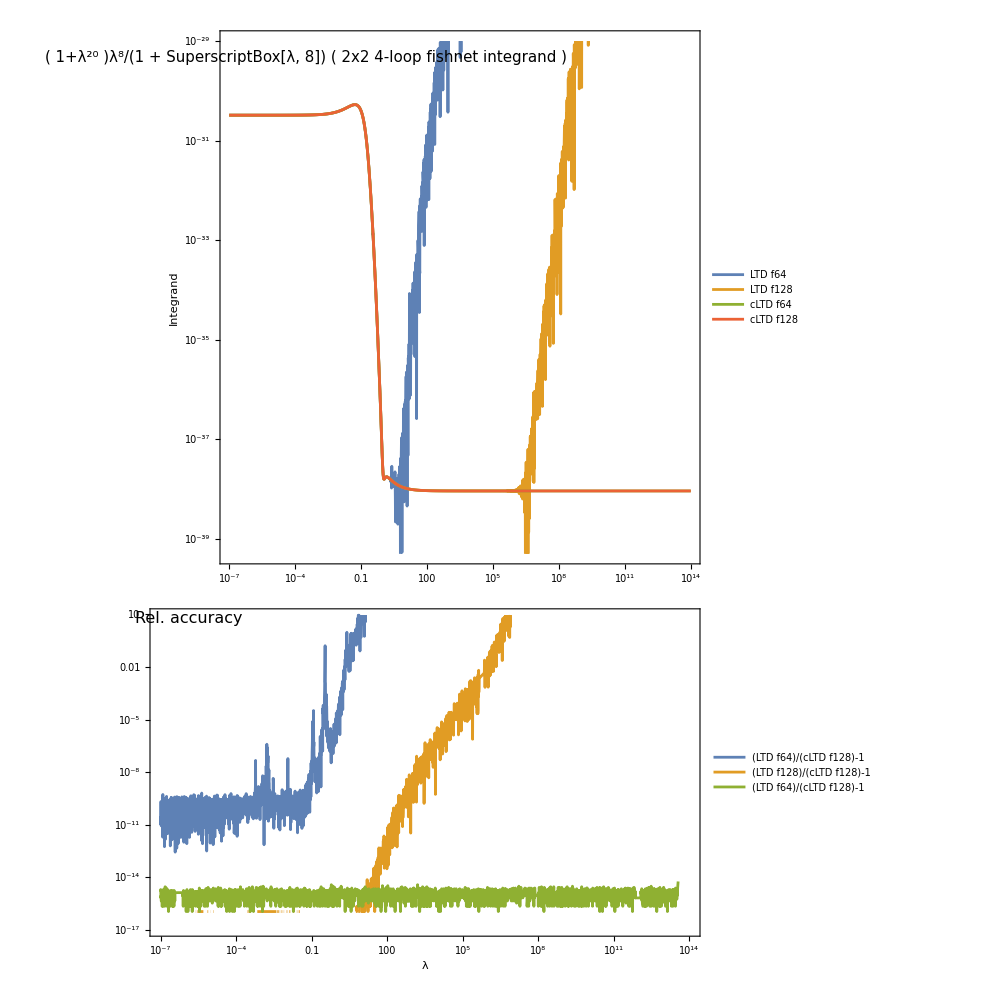

```mathematica
StabilityFigureFishnet=GraphicsColumn[{
Show[FishenetPlotGlobalView,
Graphics[Text[Style["( 1+λ^20 )λ^8/(1 + SuperscriptBox[λ, 8]) ( 2x2 4-loop fishnet integrand )",ChosenFontSize-1],Scaled[{0.18,0.95}]]]
],
Show[FishenetPlotGlobalViewSubPlot,Graphics[Text[Style["Rel. accuracy",ChosenFontSize],Scaled[{0.07,0.97}]]]]
},Spacings->{0,-10},ImageSize->{1000,1000}]
```

```mathematica
Export[NotebookDirectory[]<>"plots/stability_fishnet.pdf",StabilityFigureFishnet]
```

/Users/valentin/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/cLTD_stability/plots/stability_fishnet.pdf

```mathematica
TestLambda=4;TestF128=False;(Abs[RFM$EvaluateCut[HookFishnet2x2LTD,0,1.0,1.0,Join[ScannedMomenta[TestLambda,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->TestF128]]
/Abs[RFM$EvaluateCut[HookFishnet2x2PF,0,1.0,1.0,Join[ScannedMomenta[TestLambda,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]])-1.
```

-0.390746

```mathematica
RefreshHooks[]
```

{True,True,True,True}

```mathematica
ChosenDirection={
{(*0.1,*)0.15,0.2,0.25},
{(*0.3,*)0.35,0.4,0.45},
{(*0.5,*)0.55,0.6,0.65},
{(*0.7,*)0.75,0.8,0.85}
};
NormalisingUVPower=14;
NormalisingIRPower=2;
```

```mathematica
ChLam=10^7;(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->False]
ChLam=10^8;(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->False]
```

3.06651×10^-30+0. ⅈ

3.06651×10^-30+0. ⅈ

```mathematica
ChLam=N[10^-6];(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->False]
(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->True]
(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->False]
(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->True]
ChLam=10^-7;(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->False]
(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->True]
(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->False]
(1+(ChLam)^NormalisingUVPower)*((ChLam)^NormalisingIRPower/(1+(ChLam)^NormalisingIRPower))RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[ChLam,2,Incr->1.0],ChosenDirection],f128->True]
```

```mathematica
(* Main plot *)
NormalisingUVPower=14;
NormalisingIRPower=2;
ChosenDirection={
{(*0.1,*)0.15,0.2,0.25},
{(*0.3,*)0.35,0.4,0.45},
{(*0.5,*)0.55,0.6,0.65},
{(*0.7,*)0.75,0.8,0.85}
};
ChosenIncrement=1;
NLoops=2;
ChosenFontSize=16;
ChosenThickness=2;
ChosenPerformanceGoal="Quality";
Numerator2L6PGlobalView=LogLogPlot[{
(1+λ^NormalisingUVPower )(λ^NormalisingIRPower/(1+λ^NormalisingIRPower))Abs[
RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]],
(1+λ^NormalisingUVPower )(λ^NormalisingIRPower/(1+λ^NormalisingIRPower))Abs[
RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]],
(1+λ^NormalisingUVPower )(λ^NormalisingIRPower/(1+λ^NormalisingIRPower))Abs[
RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]],
(1+λ^NormalisingUVPower )(λ^NormalisingIRPower/(1+λ^NormalisingIRPower))Abs[
RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]]

},{λ,10^-7,10^14},
PlotLegends->Placed[{Style["LTD f64",ChosenFontSize],Style["LTD f128",ChosenFontSize],Style["cLTD f64",ChosenFontSize],Style["cLTD f128",ChosenFontSize]},{0.9,0.8}],
PlotRange->{Automatic,{1.*^-18,5*^-31}},
(*ImageSize->{1000,1000},*)
PerformanceGoal->ChosenPerformanceGoal,
AxesLabel->{None,Style["Integrand",ChosenFontSize]},
Frame->{{True,False},{True,False}},
FrameLabel->{None,None(*Style["Integrand",ChosenFontSize]*)},
TicksStyle->{Directive[FontSize->ChosenFontSize],Directive[FontOpacity->0,FontSize->ChosenFontSize]},
FrameTicksStyle->{Directive[FontSize->ChosenFontSize],Directive[FontOpacity->0,FontSize->0]},
PlotStyle->{AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness]}
];
(* Subplot *)
Numerator2L6PSubPlot=LogLogPlot[{
Abs[(Abs[RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]]
/Abs[RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1.],
Abs[(Abs[RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]]
/Abs[RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1],
Abs[(Abs[RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]]
/Abs[RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1]
},{λ,10^-7,10^14},
PlotLegends->Placed[{Style["(LTD f64)/(cLTD f128)-1 ",ChosenFontSize],Style["(LTD f128)/(cLTD f128)-1",ChosenFontSize],Style["(cLTD f64)/(cLTD f128)-1",ChosenFontSize]},{0.9,0.8}],
PlotRange->{Automatic,{10^-17,9}},
(*ImageSize->{1000,1000},*)
PerformanceGoal->ChosenPerformanceGoal,
AxesLabel->{None,None},
Frame->{{True,False},{True,False}},
FrameLabel->{Style["λ",16],None(*Style["Rel. accuracy",ChosenFontSize]*)},
TicksStyle->Directive[FontSize->ChosenFontSize],
FrameTicksStyle->Directive[FontSize->ChosenFontSize],
PlotStyle->{AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness]},
AspectRatio->1/3,
ImagePadding->{{40.,0.},{40.0,0.}}
];
```

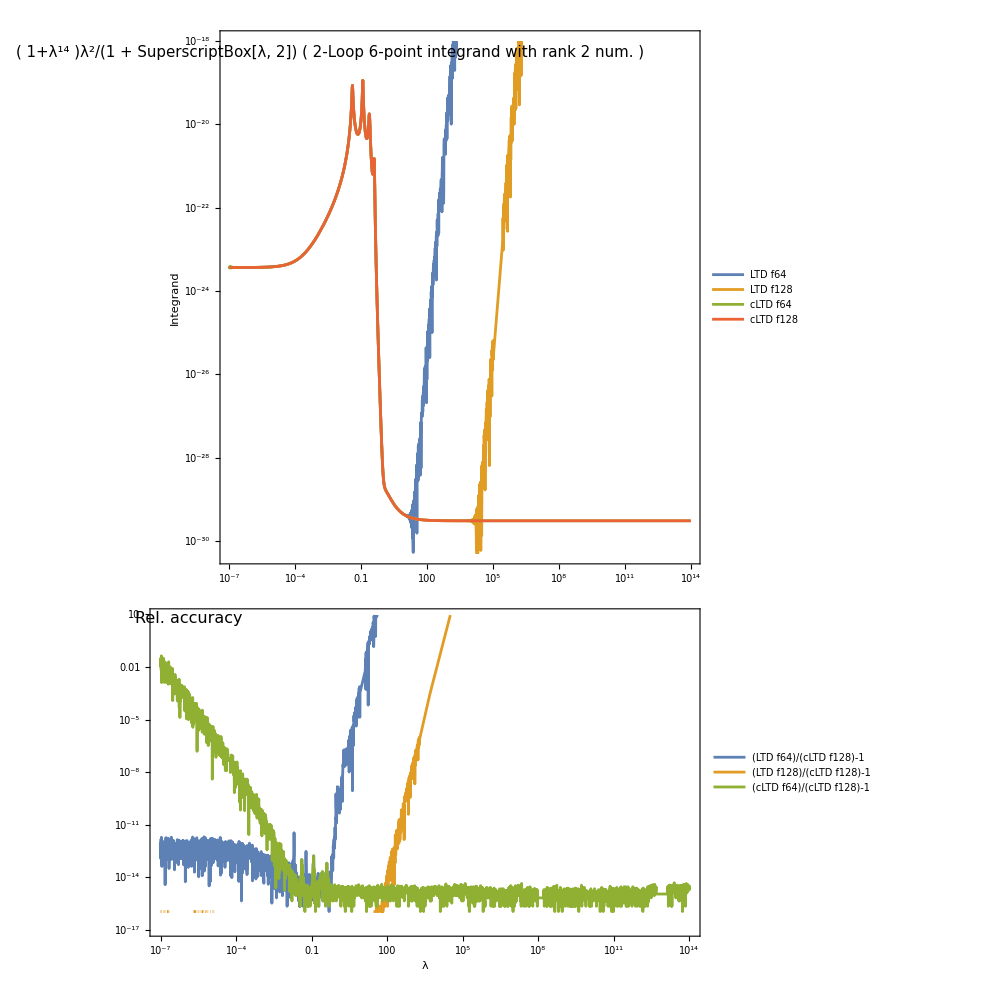

```mathematica
Figure2L6PStability=GraphicsColumn[{
Show[Numerator2L6PGlobalView,
Graphics[Text[Style["( 1+λ^14 )λ^2/(1 + SuperscriptBox[λ, 2]) ( 2-Loop 6-point integrand with rank 2 num. )",ChosenFontSize-1],Scaled[{0.23,0.96}]]]
],
Show[Numerator2L6PSubPlot,Graphics[Text[Style["Rel. accuracy",ChosenFontSize],Scaled[{0.07,0.97}]]]]
},Spacings->{0,-10},ImageSize->{1000,1000}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/stability_2L6P_with_numerator.pdf",Figure2L6PStability]
```

/Users/valentin/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/cLTD_stability//plots/stability_2L6P_with_numerator.pdf

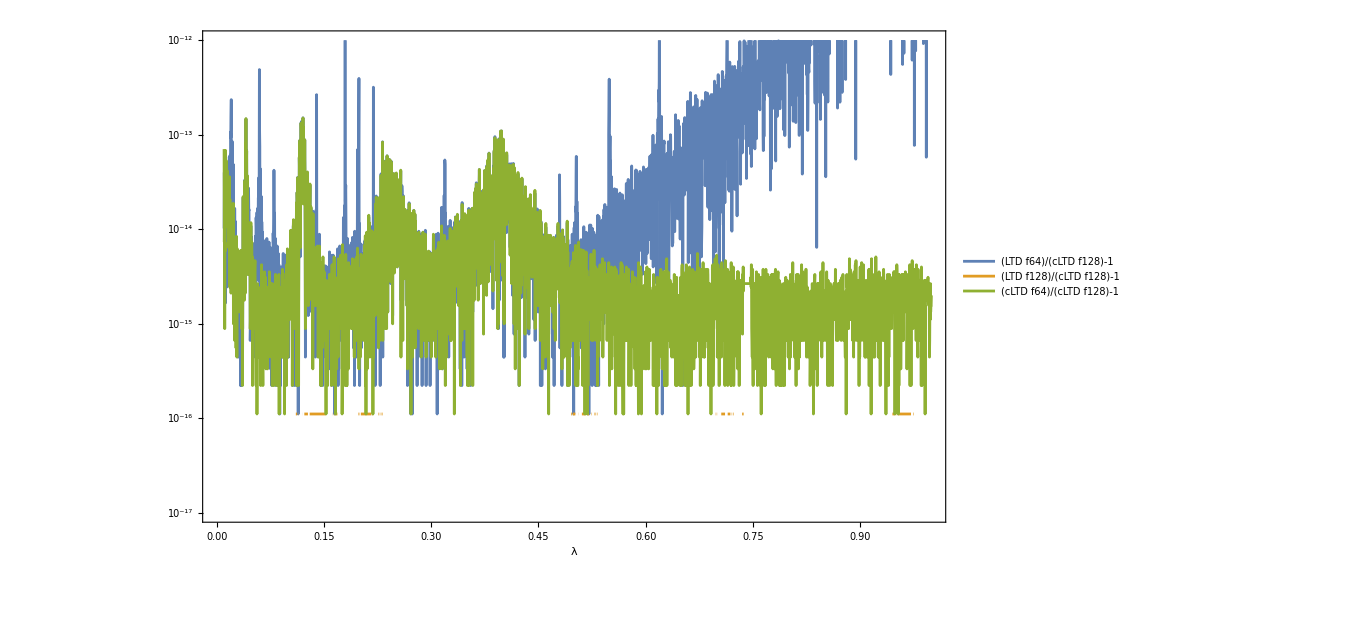

```mathematica
LogPlot[{
Abs[(Abs[RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]]
/Abs[RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1.],
Abs[(Abs[RFM$EvaluateCut[Hook2L6PLTD,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]]
/Abs[RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1],
Abs[(Abs[RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->False]]
/Abs[RFM$EvaluateCut[Hook2L6PPF,0,1.0,1.0,Join[ScannedMomenta[λ,NLoops,Incr->ChosenIncrement],ChosenDirection],f128->True]])-1]
},{λ,0.01,1},
PlotLegends->Placed[{Style["(LTD f64)/(cLTD f128)-1 ",ChosenFontSize],Style["(LTD f128)/(cLTD f128)-1",ChosenFontSize],Style["(cLTD f64)/(cLTD f128)-1",ChosenFontSize]},{0.9,0.8}],
PlotRange->{Automatic,{10^-17,10^-12}},
(*ImageSize->{1000,1000},*)
PerformanceGoal->"Quality",
AxesLabel->{None,None},
Frame->{{True,False},{True,False}},
FrameLabel->{Style["λ",16],None(*Style["Rel. accuracy",ChosenFontSize]*)},
TicksStyle->Directive[FontSize->ChosenFontSize],
FrameTicksStyle->Directive[FontSize->ChosenFontSize],
PlotStyle->{AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness],AbsoluteThickness[ChosenThickness]},
ImageSize->{1000,1000}
]
```